```mathematica
Needs["ErrorBarPlots`"]
```

DropInList lässt das von einer Liste list mit inneren Listen jedes Element von from bis to fallen (jeweils inklusive)

```mathematica
DropInList[list_,from_,to_]:=Module[{buffer=list}, For[i=0,i<Length[buffer],i++;buffer[[i]]=Drop[buffer[[i]],{from,to}]];If[from⩽to,
Return[buffer],Return["It has to be from =< to"]]]
```

ErrorBarXY erzeugt eine Liste mit ErrorBar[x[[i]],y[[i]]]
Alternativ: ErrorBarXY[listXerr_,listYerr_]=ErrorBar@@@(Partition[Flatten[Riffle[listXerr,listYerr]],2])

```mathematica
ErrorBarXY[listXerr_,listYerr_]:=Module[{buffer=listXerr}, For[i=0,i<Length[buffer],i++;buffer[[i]]=ErrorBar[listXerr[[i]],listYerr[[i]]]]; If[Length[listXerr]==Length[listYerr],
Return[buffer],Return["Length of lists not equal"]]]
```

errorPlotValue erzeugt die Punkte aus listX und listY und hängt jedem Punkt die entsprechende Errorbar[listXerr,listYerr] an

```mathematica
errorPlotValue[listX_,listY_,listXerr_,listYerr_]:=Module[{buffer=listXerr,errors,points,plotValues}, errors=ErrorBarXY[listXerr,listYerr];
points=Partition[Flatten[Riffle[listX,listY]],2];
plotValues=Partition[Riffle[points,errors],2]; If[Length[listXerr]==Length[listYerr]==Length[listX]==Length[listY],
Return[plotValues],Return["Length of lists not equal"]]]
```

errorPropNew ist für die Fehlerfortpflanzung ganzer Listen geeignet. vars={{x,dx},{y,dy}...} und func eine Funktion die von x,y... abhängt. Es wird die zugehörige Fehlerfunktion zurückgegeben. Speicher diese unter einem Namen ab zB errFkt.
Nutze errFkt[list_x,list_dx,list_y,list_dy,...]

```mathematica
errorPropNew[func_,vars_]:=Module[{derivs=Table[0,{Length[vars]}],funcErrorForm,parameter,errFunction},

For[ii=1,ii≤Length[vars],ii++,derivs[[ii]]=D[func,vars[[ii,1]]];];
parameter=Flatten[vars];
funcErrorForm=Sqrt[Sum[(derivs[[ii]]*vars[[ii,2]])^2,{ii,Length[vars]}]];
errFunction=Function@@{parameter,funcErrorForm};
Return[errFunction];];
```

Wendet f auf die n-te Komponenten jedes Punktes in g an. Alternativ {f@First[#], Last[#]} &/@ g;

```mathematica
MapAt[(f[#])&,#,n]&/@g
```

Ab hier ein Beispiel

```mathematica
g={{0.6*10^-2,0.625*10^-2},{0.8*10^-2,0.675*10^-2},{0.95*10^-2,0.718*10^-2},{1.3*10^-2,0.38*10^-2},{2.0*10^-2,0.203333*10^-2}};
```

```mathematica
errgXwert={0.025*10^-2,0.025*10^-2,0.025*10^-2,0.025*10^-2,0.025*10^-2}
```

{0.00025,0.00025,0.00025,0.00025,0.00025}

```mathematica
errgYwert={(0.025*10^-2)/12,(0.025*10^-2)/12,(0.025*10^-2)/11,(0.025*10^-2)/17,(0.025*10^-2)/30}
```

{0.0000208333,0.0000208333,0.0000227273,0.0000147059,8.33333×10^-6}

```mathematica
gXwert=DropInList[g,2,2]
```

{{0.006},{0.008},{0.0095},{0.013},{0.02}}

```mathematica
gYwert=DropInList[g,1,1]
```

{{0.00625},{0.00675},{0.00718},{0.0038},{0.00203333}}

Transformation der x-Achse

```mathematica
f[x_]:=1/x
```

```mathematica
durchgXwert=Map[f,gXwert]
```

{{166.667},{125.},{105.263},{76.9231},{50.}}

Fehlerfortpflanzung:Die zu f zugehörige Transformation der Fehler der x-Werte

```mathematica
errFkt=errorPropNew[f[x],{{x,dx}}]
```

Function[{x,dx},√(dx^2/x^4)]

```mathematica
errdurchgXwert=Flatten[errFkt[gXwert,errgXwert]]
```

{6.94444,3.90625,2.77008,1.47929,0.625}

Erstellen der Errorbars:Verknüpfung der transformierten x-Werte-Fehler mit den alten y-Werten-Fehlern

```mathematica
plotThis=errorPlotValue[durchgXwert,gYwert,errdurchgXwert,errgYwert]
```

{{{166.667,0.00625},ErrorBar[6.94444,0.0000208333]},{{125.,0.00675},ErrorBar[3.90625,0.0000208333]},{{105.263,0.00718},ErrorBar[2.77008,0.0000227273]},{{76.9231,0.0038},ErrorBar[1.47929,0.0000147059]},{{50.,0.00203333},ErrorBar[0.625,8.33333×10^-6]}}

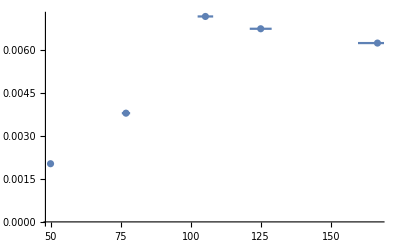

```mathematica
ErrorListPlot[plotThis]
```